## Constants

```mathematica
(*make sure to run appendix_benchmark_values.nb first*)
```

```mathematica
me=5.11*10^5; (*eV*)
α=1/137;
QX= 2;
REarth = 32.322 *10^12; (*eV^-1*)
vAvg [mX_]:= 3.669*10^ (-5)*Sqrt[5*10^9/mX]; (*using mass of Helium = 5 GeV*)
nF(*[mX_]*):= 2.3*10^(-17)(*0.1*3841/mX*); (*eV^3*)
T= 119(*2.643*); (*eV*)
MEarth = 3.35041*10^(60); (*eV*)
G = 6.70883*10^(-57);(*eV^-2*)
TEarth = 0.345; (*eV*)
mMeeV= currentfoverv*511/1000*10^-3*10^(9);
mHeV = mHGeV[currentfoverv]*10^(9);
mHeeV=4*mHGeV[currentfoverv]*10^(9); (*eV*)
nFHeeV=currentY (3/10)/(mHeeV*10^(-9))*5/100*7.68*10^(-15);
nFMeeV=currentY (3/10)/(mHeeV*10^(-9))*(5*2)/100*7.68*10^(-15);
QHe=2;
QH=1;
v0HeeV=SetPrecision[v0kmsHeDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11)(*natural units*),20];
v0EeV=v0kmsEDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11)(*natural units*); 
fHeDisk[v_,T_,mX_]:=(correctf[v/(10^5*3.33*10^(-11))]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsHeDisk[currentfoverv,currentY]})/(10^5*3.33*10^(-11));
```

## Make Target List

```mathematica
(*Note on conventions: all atoms named by normal abbr. OR if abbr. is 1 letter, by first 2 letters of atom name*)
(*find number density in (eV)^-3 from mass fraction, mass in amu's*)
findnT[massfrac_,amass_]:=massfrac/amass*(5.97217*10^(24))/(1.66054*10^(-27))/(1.4145*10^(41)); 
(*find mass of atom in eV*)
findmT[amass_]:=amass*9.314*10^(8);

(* {Z, massfrac in Earth, mass in amu, number density, mass in eV}*)
OX = {8,.297,15.999,findnT[.297,15.999],findmT[15.999]};
MG = {12,.154,24.305,findnT[.154,24.305],findmT[24.305]};
SI= {14,.161,28.085,findnT[.161,28.085],findmT[28.085]};
FE={26,.319,55.845,findnT[.319,55.845],findmT[55.845]};
AL = {13,.0159,26.982,findnT[.0159,26.982],findmT[26.982]};
CA = {20,.0171,40.078,findnT[.0171,40.078],findmT[40.078]};
NI = {28,.0182,58.693,findnT[.0182,58.693],findmT[58.693]};
HY = {1,.00026,1.008,findnT[.00026,1.008],findmT[1.008]};
SU= {16,.00635,32.06,findnT[.00635,32.06],findmT[32.06]};
CR = {24,.0047,51.996,findnT[.0047,51.996],findmT[51.996]};
NA = {11,.0018,22.990,findnT[.0018,22.990],findmT[22.990]};
CA= {6,.00073,12.011,findnT[.00073,12.011],findmT[12.011]};
PH = {15,.00121,30.974,findnT[.00121,30.974],findmT[30.974]};
```

```mathematica
targList = {OX,MG,SI,FE,AL,CA,NI,HY,SU,CR,NA,CA,PH};
```

## Find Capture Rates

```mathematica
v2esc[QEarth_,mX_]:=2*G*MEarth/REarth-1/(2*Pi)*QEarth*QX/(REarth*mX);
```

```mathematica
SSfactorContrib[target_,mX_,ϵ_]:=If[(4*target[[5]]^2*mX*(T)/((target[[5]]+mX)^2*(me*α)^2))>1,target[[4]]*mX*Pi*α^2*ϵ^2*QX^2*target[[1]]^2/target[[5]]*Log[(4*target[[5]]^2*mX*(T))/((target[[5]]+mX)^2*(me*α)^2)],0];
```

```mathematica
SSfactor[targetList_,mX_,ϵ_]:=Sum[SSfactorContrib[targetList[[i]],mX,ϵ],{i,1,Length[targetList]}];
```

```mathematica
v2cap[target_,mX_,ϵ_,v2esc_]:=(8*SSfactorContrib[target,mX,ϵ]*REarth/mX^2+v2esc^2)^(1/2);
```

```mathematica
vmin[QEarth_,mX_]:= If[v2esc[QEarth,mX]>0,0,Sqrt[-v2esc[QEarth,mX]]];
```

```mathematica
nFRSoftContrib[target_,mX_,ϵ_,QEarth_]:=nF/(*[mX]*)REarth*NIntegrate[Sqrt[v^2+v2esc[QEarth,mX]]*fH[v,T,mX],{v,0(*vmin[QEarth,mX]*),Sqrt[v2cap[target,mX,ϵ,v2esc[QEarth,mX]]-v2esc[QEarth,mX]]}];
```

```mathematica
nFRSoft[targetList_,mX_, ϵ_, QEarth_]:= Sum[nFRSoftContrib[targetList[[i]],mX,ϵ,QEarth],{i,1,Length[targetList]}];
```

```mathematica
(*testing*)
```

```mathematica
reg=10^-6;
vmini[ϵ_,target_]:=SetPrecision[(ϵ^2*4*Pi*α^2*QHe^2*REarth*target[[4]]/mHeeV^2)^(1/4),50];
fvHeTest[vmin_,vmax_,v0_,vesc_]:=NIntegrate[v^2*Sqrt[v^2+vesc^2]*Exp[-3v^2/2/v0^2],{v,vmin,vmax}]/NIntegrate[v^2Exp[-3v^2/2/v0^2],{v,0,10v0}];fHeHaloTest[v_]:=(correctf[v/(3.33*10^(-6))]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsHeHalo[currentfoverv,currentY]})/3.33*10^(-6);
effσHe[vmin_,vmax_]:=NIntegrate[v*(4Pi*α^2*QHe^2)/(mHeeV^2*v^4)*fHeHaloTest[v],{v,vmin,vmax}]/NIntegrate[fHeHaloTest[v],{v,0,10*v0HeeV}];
nFRHardContTest[target_,mX_,eps_,QEarth_]:=(target[[4]]*nFHeeV*eps^2*SetPrecision[effσHe[vmini[eps,target],Sqrt[(v2esc[QEarth,mX]*(mHeeV+target[[5]])^2/(mHeeV-target[[5]])^2)-v2esc[QEarth,mX]]+reg],50])+(nFHeeV*fvHeTest[0,vmini[eps,target],v0HeeV,Sqrt[v2esc[QEarth,mX]]]/REarth);
```

```mathematica
(*end testing*)
```

```mathematica
σHT[target_,mX_,ϵ_,v2_]:=(2*Pi*α^2*ϵ^2/(target[[5]]*v2^2)^2)*((target[[5]]+mX)^2/(2*mX^2));
```

```mathematica
nFRHardTest[target_,mX_,ϵ_]:=(nF*ϵ^2*SetPrecision[effσvHe[target,mX,ϵ,vmin[target,mX,ϵ],√(v2esc[0,mX](((mHe+16)/(16-mHe))^2-1))+reg],50])*target[[4]]+nF*NIntegrate[fH[v,T,mX],{v,0,vmin[target,mX,ϵ]}]/REarth
```

```mathematica
nFRHard[targetList_,mX_,ϵ_,QEarth_]:=nF[mX]*Sum[(nFRHardContrib[targetList[[i]],mX,ϵ,QEarth]*targetList[[i]][[4]]),{i,1,Length[targetList]}];
```

```mathematica
Peject[mX_]:= Integrate[fH[v,TEarth,mX],{v,,Infinity}];
```

```mathematica
chargeAccum[targetList_,mX_,ϵ_,QEarth_,timeInt_]:=(nFRSoft[targetList,mX,ϵ,QEarth]+nFRHard[targetList,mX,ϵ,QEarth])*4/3*Pi*REarth^3*timeInt;
```

```mathematica
p1=LogPlot[nFRSoftContrib[OX,5*10^9,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True];
```

```mathematica
nFRSoftContrib[OX,5*10^9,10^-10,0]
```

1.84726×10^-37

```mathematica
nFRHardContTest[OX,mHeeV,10^(-10),0]
```

General::munfl: Exp[-6.19835×10^9] is too small to represent as a normalized machine number; precision may be lost.

8.54917×10^-40

```mathematica
p2=LogPlot[1.47*10^9/(4.72*10^8)nFRHardContTest[OX,mHeeV,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True];
```

General::munfl: Exp[-6.19835×10^9] is too small to represent as a normalized machine number; precision may be lost.

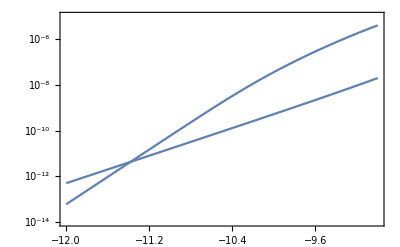

```mathematica
Show[p1,p2]
```

### Testing

```mathematica
NIntegrate[v*fH[v,T,10^9],{v,0(*vmin[QEarth,mX]*),Sqrt[v2cap[OX,10^9,10^(-14),v2esc[0,10^9]]-v2esc[0,10^9]]}]
```

8.22258×10^-23

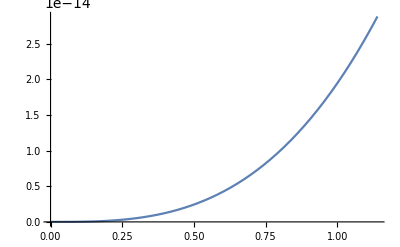

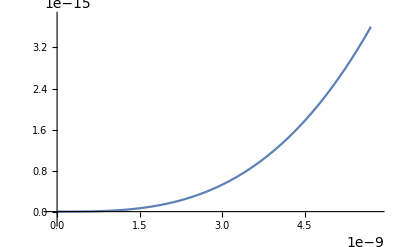

```mathematica
Plot[v*fH[v,T,10^9],{v,0,Sqrt[v2cap[OX,10^9,10^(-14),v2esc[0,10^9]]-v2esc[0,10^9]]}]
```

```mathematica
Sqrt[v2cap[OX,10^9,10^(-14),v2esc[0,10^9]]-v2esc[0,10^9]]
```

1.14054×10^-8

```mathematica
SSfactorContrib[OX,10^9,10^(-14)]
```

1.3994×10^-21

```mathematica
nFRSoftContrib[OX,10^9,10^(-14),0]
```

2.55095×10^-49

```mathematica
nFRSoft[targList,10^11,10^(-14),0]
```

8.45861×10^-49

```mathematica
nFRHard[targList,10^11,10^(-14),0]
```

2.3×10^-17[100000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},100000000000,1/100000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},100000000000,1/100000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},100000000000,1/100000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},100000000000,1/100000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},100000000000,1/100000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},100000000000,1/100000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},100000000000,1/100000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},100000000000,1/100000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},100000000000,1/100000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},100000000000,1/100000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},100000000000,1/100000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},100000000000,1/100000000000000,0])

```mathematica
chargeAccum[targList,10^9,10^(-14),0,10^37]
```

1.41444×10^78 (6.8905×10^-49+2.3×10^-17[1000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},1000000000,1/100000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},1000000000,1/100000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1000000000,1/100000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},1000000000,1/100000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},1000000000,1/100000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},1000000000,1/100000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},1000000000,1/100000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},1000000000,1/100000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},1000000000,1/100000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},1000000000,1/100000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},1000000000,1/100000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},1000000000,1/100000000000000,0]))

```mathematica
chargeAccum[targList,10^9,10^(-12),0,10^37]
```

1.41444×10^78 (6.88806×10^-43+2.3×10^-17[1000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},1000000000,1/1000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},1000000000,1/1000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1000000000,1/1000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},1000000000,1/1000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},1000000000,1/1000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},1000000000,1/1000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},1000000000,1/1000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},1000000000,1/1000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},1000000000,1/1000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},1000000000,1/1000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},1000000000,1/1000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},1000000000,1/1000000000000,0]))

```mathematica
chargeAccum[targList,10^9,10^(-13),0,10^37]
```

1.41444×10^78 (6.89047×10^-46+2.3×10^-17[1000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},1000000000,1/10000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},1000000000,1/10000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1000000000,1/10000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},1000000000,1/10000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},1000000000,1/10000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},1000000000,1/10000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},1000000000,1/10000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},1000000000,1/10000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},1000000000,1/10000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},1000000000,1/10000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},1000000000,1/10000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},1000000000,1/10000000000000,0]))

```mathematica
chargeAccum[targList,10^7,10^(-11),0,10^37]
```

1.41444×10^78 (1.49598×10^-40+2.3×10^-17[10000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},10000000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},10000000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},10000000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},10000000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},10000000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},10000000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},10000000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},10000000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},10000000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},10000000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},10000000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},10000000,1/100000000000,0]))

```mathematica
chargeAccum[targList,10^5,10^(-11),0,10^37]
```

1.41444×10^78 (4.26096×10^-42+2.3×10^-17[100000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},100000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},100000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},100000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},100000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},100000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},100000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},100000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},100000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},100000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},100000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},100000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},100000,1/100000000000,0]))

```mathematica
chargeAccum[targList,10,10^(-11),0,10^37]
```

1.41444×10^78 (0.+2.3×10^-17[10] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},10,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},10,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},10,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},10,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},10,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},10,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},10,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},10,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},10,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},10,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},10,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},10,1/100000000000,0]))

```mathematica
chargeAccum[targList,10^10,10^(-11),0,10^37]
```

1.41444×10^78 (8.60545×10^-40+2.3×10^-17[10000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},10000000000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},10000000000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},10000000000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},10000000000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},10000000000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},10000000000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},10000000000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},10000000000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},10000000000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},10000000000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},10000000000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},10000000000,1/100000000000,0]))

```mathematica
(.02*2*T/10^20+ 2*G*MEarth/REarth)*(2*Pi*REarth*10^20/QX)
```

1.41229×10^25

```mathematica
chargeAccum[targList,10^9,10^(-25),0,10^37]
```

1.41444×10^78 (0.+2.3×10^-17[1000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},1000000000,1/10000000000000000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},1000000000,1/10000000000000000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1000000000,1/10000000000000000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},1000000000,1/10000000000000000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},1000000000,1/10000000000000000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},1000000000,1/10000000000000000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},1000000000,1/10000000000000000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},1000000000,1/10000000000000000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},1000000000,1/10000000000000000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},1000000000,1/10000000000000000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},1000000000,1/10000000000000000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},1000000000,1/10000000000000000000000000,0]))

```mathematica
chargeAccum[targList,10^20,10^(-11),0,10^37]
```

1.41444×10^78 (0.+2.3×10^-17[100000000000000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},100000000000000000000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},100000000000000000000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},100000000000000000000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},100000000000000000000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},100000000000000000000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},100000000000000000000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},100000000000000000000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},100000000000000000000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},100000000000000000000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},100000000000000000000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},100000000000000000000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},100000000000000000000,1/100000000000,0]))

```mathematica
nFRHard[targList,10^20,10^(-11),0]
```

2.3×10^-17[100000000000000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},100000000000000000000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},100000000000000000000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},100000000000000000000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},100000000000000000000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},100000000000000000000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},100000000000000000000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},100000000000000000000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},100000000000000000000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},100000000000000000000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},100000000000000000000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},100000000000000000000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},100000000000000000000,1/100000000000,0])

```mathematica
nFRSoft[targList,10^20,10^(-11),0]
```

0.

```mathematica
nFRHardContrib[OX,10^20,10^(-11),0]
```

nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},100000000000000000000,1/100000000000,0]

```mathematica
σHT[OX,10^20,10^(-11),v2esc[0,10^20]*(((10^20+OX[[5]])/Abs[10^20-OX[[5]]])^2-1)]
```

1.59584×10^26

```mathematica
Plot[σHT[OX,10^20,10^-11,v2],{v2,0,10^(-100)}]
```

General::munfl: (6.21878×10^-200)^2 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: (6.21879×10^-194)^2 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: (2.48503×10^-193)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
chargeAccum[targList,10^10,10^(-11),0,10^37]
```

1.41444×10^78 (8.60545×10^-40+2.3×10^-17[10000000000] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},10000000000,1/100000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},10000000000,1/100000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},10000000000,1/100000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},10000000000,1/100000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},10000000000,1/100000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},10000000000,1/100000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},10000000000,1/100000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},10000000000,1/100000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},10000000000,1/100000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},10000000000,1/100000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},10000000000,1/100000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},10000000000,1/100000000000,0]))

```mathematica
critCharge[mX_]:=(.04*T/mX+2*G*MEarth/REarth)*(2*Pi*REarth*mX/QX);
```

```mathematica
critCharge[1.5*10^14]
```

2.11849×10^19

```mathematica
chargeAccum[targList,1.5*10^14,10^(-26),0,10^37]
```

1.41444×10^78 (0.+2.3×10^-17[1.5×10^14] (6.55832×10^6 nFRHardContrib[{1,0.00026,1.008,6.55832×10^6,9.38851×10^8},1.5×10^14,1/100000000000000000000000000,0]+3.09068×10^6 nFRHardContrib[{6,0.00073,12.011,1.54534×10^6,1.1187×10^10},1.5×10^14,1/100000000000000000000000000,0]+4.72002×10^8 nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1.5×10^14,1/100000000000000000000000000,0]+1.99073×10^6 nFRHardContrib[{11,0.0018,22.99,1.99073×10^6,2.14129×10^10},1.5×10^14,1/100000000000000000000000000,0]+1.61103×10^8 nFRHardContrib[{12,0.154,24.305,1.61103×10^8,2.26377×10^10},1.5×10^14,1/100000000000000000000000000,0]+1.49831×10^7 nFRHardContrib[{13,0.0159,26.982,1.49831×10^7,2.5131×10^10},1.5×10^14,1/100000000000000000000000000,0]+1.45758×10^8 nFRHardContrib[{14,0.161,28.085,1.45758×10^8,2.61584×10^10},1.5×10^14,1/100000000000000000000000000,0]+993271. nFRHardContrib[{15,0.00121,30.974,993271.,2.88492×10^10},1.5×10^14,1/100000000000000000000000000,0]+5.03605×10^6 nFRHardContrib[{16,0.00635,32.06,5.03605×10^6,2.98607×10^10},1.5×10^14,1/100000000000000000000000000,0]+2.29831×10^6 nFRHardContrib[{24,0.0047,51.996,2.29831×10^6,4.84291×10^10},1.5×10^14,1/100000000000000000000000000,0]+1.4524×10^8 nFRHardContrib[{26,0.319,55.845,1.4524×10^8,5.2014×10^10},1.5×10^14,1/100000000000000000000000000,0]+7.88433×10^6 nFRHardContrib[{28,0.0182,58.693,7.88433×10^6,5.46667×10^10},1.5×10^14,1/100000000000000000000000000,0]))

```mathematica
nFRSoftContrib[OX,10^9,10^(-11),0]
```

2.45118×10^-40

```mathematica
v2cap[OX,10^9,10^(-11),1.39*10^(-9)]
```

1.51458×10^-9

```mathematica
v2esc[0,10^9]
```

1.39084×10^-9

```mathematica
SSfactorContrib[OX,10^9,10^(-11)]
```

1.3994×10^-15

```mathematica
nFRHardContrib[OX,10^9,10^(-11),0]
```

nFRHardContrib[{8,0.297,15.999,4.72002×10^8,1.49015×10^10},1000000000,1/100000000000,0]

```mathematica
σHT[OX,10^20,10^(-11),((v2cap[OX,10^20,10^(-11),v2esc[0,10^20]]-v2esc[0,10^20])+v2esc[0,10^20])]*Sqrt[(v2cap[OX,10^20,10^(-11),v2esc[0,10^20]]-v2esc[0,10^20])]*fH[Sqrt[(v2cap[OX,10^20,10^(-11),v2esc[0,10^20]]-v2esc[0,10^20])],T,10^20]
```

0.

```mathematica
σHT[OX,10^20,10^(-11),(v2esc[0,10^20]*(((10^20+OX[[5]])/(10^20-OX[[5]]))^2-1))]*Sqrt[v2esc[0,10^20]*(((10^20+OX[[5]])/(10^20-OX[[5]]))^2-1)]*fH[Sqrt[v2esc[0,10^20]*(((10^20+OX[[5]])/(10^20-OX[[5]]))^2-1)],T,10^20]
```

5.22613×10^25

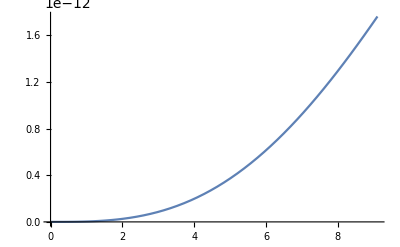

```mathematica
Plot[σHT[targList[[13]],10^20,10^(-11),(v^2+v2esc[0,10^20])]*v*fH[v,T,10^20],{v,Sqrt[(v2cap[OX,10^20,10^(-11),v2esc[0,10^20]]-v2esc[0,10^20])],Sqrt[v2esc[0,10^20]*(((10^20+OX[[5]])/(10^20-OX[[5]]))^2-1)]}]
```

```mathematica
Sqrt[v2cap[OX,10^9,10^(-14),v2esc[0,10^(9)]]-v2esc[0,10^(9)]]
```

1.14054×10^-8

## Charge Shielding (Disk)

```mathematica
alphaH = 0;
alphaHe = 2*nFHeeV/(4*nFHeeV+nFMeeV);
alphaE = -nFMeeV/(4*nFHeeV+nFMeeV);
beta0 = 10*10^23/(4*Pi*REarth^3/3)/(4*nFHeeV+nFMeeV);
phiE = beta0/(2*alphaH+3*alphaHe);
```

#### Delta Function Case (Analytic + Numeric)

#### Analytic

```mathematica
A1d=1;
rhoE = beta0/(2*alphaH+3*alphaHe)/5;
```

```mathematica
phiShIntnewA[r_,rMax_]:=((2r^2-rMax^2)-Sqrt[(2r^2-rMax^2)^2+32(r^4-rMax^2r^2)])/(16r^2)/A1d;
RMaxonewA=rMax/.NSolve[{phiShIntnewA[REarth,rMax]==rhoE,rMax>0},rMax][[1]];
phiShnewA[r_]:=Piecewise[{{rhoE,r<=REarth},{phiShIntnewA[r,RMaxonewA],REarth<r<RMaxonewA},{0,r>=RMaxonewA}}]
deltaV=20;
vMax=100;
```

```mathematica
(*make a plot with the analytic delta function ditribution potentials for different values of v_inf*)
A1dList = {{1,Purple},{2,Magenta},{3,Red},{5,Orange},{6,Black},{0.7,Blue},{0.5,Cyan},{0.3,Green},{0.01,Gray},{0.001,Brown}};
PlotList1d=List[];

Do[phiShIntnewA[r_,rMax_]:=((2r^2-rMax^2)-Sqrt[(2r^2-rMax^2)^2+32(r^4-rMax^2r^2)])/(16r^2)/A1dList[[i,1]];
RMaxonewA=rMax/.NSolve[{phiShIntnewA[REarth,rMax]==rhoE,rMax>0},rMax][[1]];
(*Print[RMaxonewA/REarth]*);
phiShnewA[r_]:=Piecewise[{{rhoE,r<=REarth},{phiShIntnewA[r,RMaxonewA],REarth<r<RMaxonewA},{0,r>=RMaxonewA}}];
plotConstVnewA = Plot[rat^2*phiShnewA[REarth rat],
{rat,0.995,1.02},
PlotStyle->A1dList[[i,2]]];
(*Print[(1+A1dList[[i,1]]phiShnewA[REarth]-RMaxonewA^2/REarth^2)];*)
AppendTo[PlotList1d,plotConstVnewA],{i,Length[A1dList]}]
```

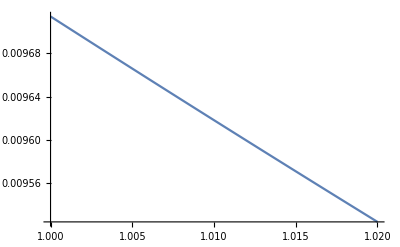

```mathematica
noScreening=Plot[rhoE/rat,{rat,1,1.02}]
```

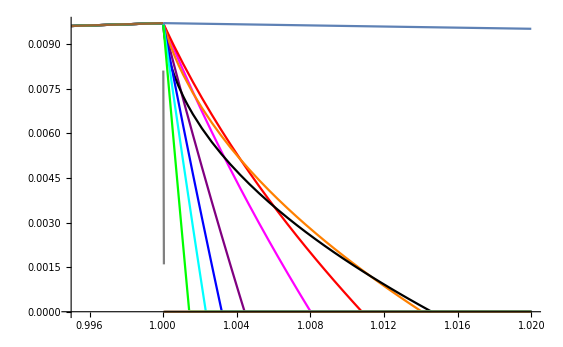

```mathematica
Show[PlotList1d(*,PlotRange->{{0.999,1.00006},{0,0.002}}*),noScreening]
```

#### Numeric

```mathematica
smallrETerm[RMax_,r_,phi_,phiRMax_]:=Piecewise[{{0,r>RMax},{Re[Sqrt[1+phi]Sqrt[1+phi-RMax^2/r^2(1+phiRMax)]],r<=RMax}}];
```

```mathematica
rList=Table[1- 10^-5 i,{i,2000}];
rhoConstVList={};
indexConstV=1;
rhoEarth=beta0/(2*alphaH+3*alphaHe);
While[True,root=phi/.FindRoot[alphaHe*(1-2 *vrat*phi)+alphaE*(1+ vrat*phi-smallrETerm[1,rList[[indexConstV]], vrat*phi,0]),{phi,0.00001,rhoEarth},Method->"Brent"];
 If[root>=rhoEarth-10^(-4),Break[]];AppendTo[rhoConstVList,{rList[[indexConstV]],root}];indexConstV++]
```

```mathematica
(*RMax initially set to 1, rescale to match REarth*)
rescaleRMaxVConst[elem_]:={elem[[1]]/rhoConstVList[[-1,1]],elem[[2]]};
rescaledrhoConstVList=rescaleRMaxVConst/@rhoConstVList;
```

```mathematica
numericalConstV=ListPlot[rescaledrhoConstVList];
```

```mathematica
numericalConstVURS = ListPlot[rhoConstVList] (*not rescaled*);
```

```mathematica
rescaleVURS[elem_]:={elem[[1]],2*elem[[2]]/3};
numericalConstVURSR=ListPlot[Map[rescaleVURS,rhoConstVList]];
```

#### MB Distribution Case

```mathematica
(*create lists for recursion over vinf to find RMax(vinf), also define MB distribution weight factor to match velocities in vInfList*)
vInfList=PowerRange[1/20,4,1+2/10];
(*MBfactor[i_,T_,mX_]:=v0HeeV*deltaVL*fHeDisk[vInfList[[i]],T,mX];*)
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];
MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
(*helper functions for the recursion below. *)
```

```mathematica
derivF[i_,RMax_,r_,phi_?NumericQ,n_]:=Re[N[((-3+9phi)-Sum[MBfactor[k]/(2 √((vInfList[[k]])^2 + phi)vInfList[[k]]),{k,1,Length[vInfList]}])/n+((MBfactor[i]/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];
derivF[i_,RMax_,r_,phi_?NumericQ,n_]:=Re[N[(-4+8phi-14 phi^2)/n+((MBfactor[i]/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];complexF[i_,RMax_,r_]:=N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];
rootF[i_,RMax_,r_,phi_?NumericQ,n_]:=Re[N[(-4phi+4 phi^2-14/3 phi^3)/n+MBfactor[i]/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];
```

```mathematica
(* start of recursion to scan over different r's to find escape potential *)
phiList={{1,0}};
RMaxList={{1,0}};
minPoint =SetPrecision[ 0.9,20];
pointNumber=10000;
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]]],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
phiNew=phi/.res;
If[phiNew>2phiE/3,
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];
```

1

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

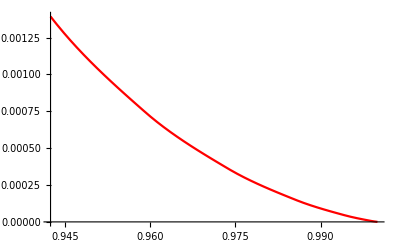

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```